#### Finite Well - Even Bound States

```mathematica
Manipulate[{Show[Plot[Tan[z],{z,0,(5 Pi)/2},PlotRange->5],Plot[((z0/z)^2-1)^(1/2),{z,0,(5 Pi)/2},PlotRange->5]]},{z0,0,10}]
```

#### Finite Well - Odd Bound States

```mathematica
Manipulate[{Show[Plot[Cot[z],{z,0,(5 Pi)/2},PlotRange->5],Plot[-((z0/z)^2-1)^(1/2),{z,0,(5 Pi)/2},PlotRange->5]]},{z0,0,10}]
```

Syntax::bktmcp: Expression "Show[Plot[Tan[(90 √(2*0.06*(E+240*10^-3)))/(4.14*10^-15)],{E,0,10},PlotRange->1000],Plot[Tan[(90 √(2*0.06*(E+240*10^-3)))/(4.14*10^-15)],{E,0,10},PlotRange->1000]" has no closing "]".

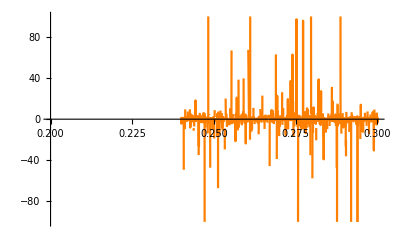

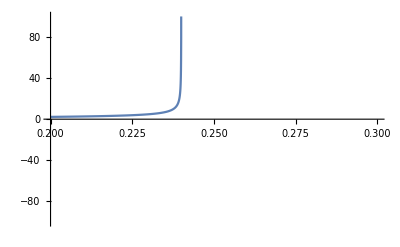

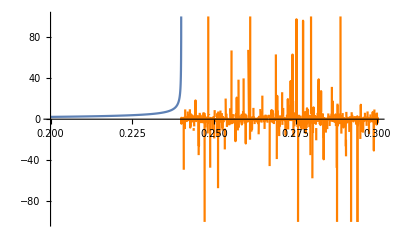

```mathematica
g1=Plot[Tan[(90 √(2*0.06*(m-(240*10^-3))))/(2*4.14*10^-15)],{m,0.2,0.3},PlotRange->100,PlotStyle->Orange]
g2=Plot[√(-m/(m-240*10^-3)),{m,0.2,0.3},PlotRange->100]
Show[g1,g2]
```

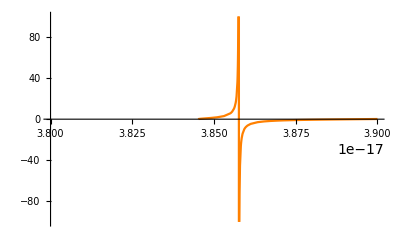

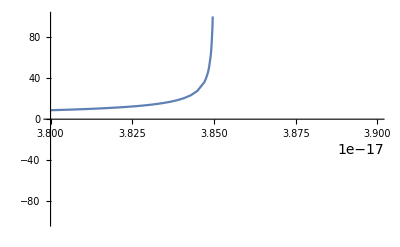

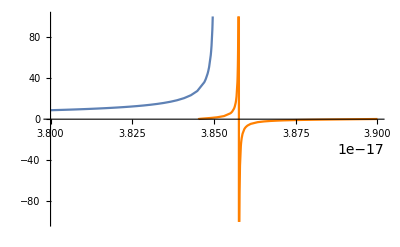

```mathematica
g3=Plot[Tan[((9*10^-9)*√(2*5.46563014*10^-32*(m-(3.8452*10^-17))))/(6.670715*10^-34)],{m,3.8*10^-17,3.9*10^-17},PlotRange->100,PlotStyle->Orange]
g4=Plot[√(-m/(m-3.85*10^-17)),{m,3.8*10^-17,3.9*10^-17},PlotRange->100]
Show[g3,g4]
```

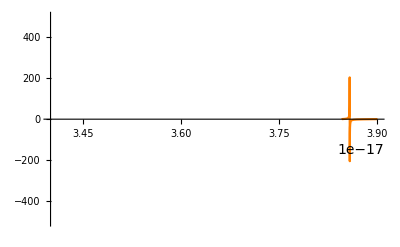

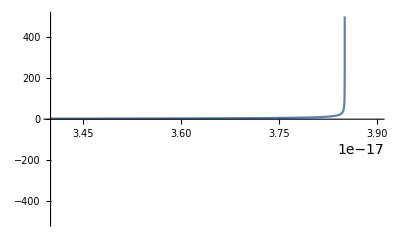

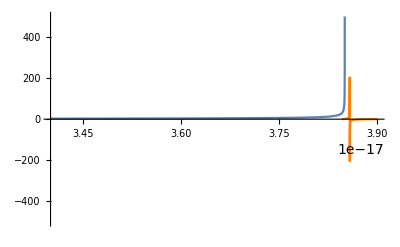

```mathematica
g3=Plot[Tan[((9*10^-9)*√(2*5.46563014*10^-32*(m-(3.8452*10^-17))))/(6.670715*10^-34)],{m,3.4*10^-17,3.9*10^-17},PlotRange->500,PlotStyle->Orange]
g4=Plot[√(-m/(m-3.85*10^-17)),{m,3.4*10^-17,3.9*10^-17},PlotRange->500]
Show[g3,g4]
```

```mathematica
{Show[Plot[Tan[z],{z,0,1*10^-17},PlotRange->5],Plot[((((4.5*10^-9*√(-2*5.47*10^-32*3.45*10^-17))/(6.67*10^-34))/z)^2-1)^(1/2),{z,0,1*10^-20},PlotRange->5]]}
```

```mathematica
{}
```